# 2 DEG Magneto - electric Properties

## Normalized energy band broad diagonal elements ( l=0)

#### Gauss-Hermite Function χ_N

```mathematica
χ[y_?NumericQ,N_?NumericQ]:= Exp[-y^2/2]/(√(2^N*N!*√π))HermiteH[N,y];
```

#### Landau Level N = 0 and E=0

```mathematica
Q00:= χ[2.342*k2,0]*χ[2.342*(k1-k2),0];
A00[k1_?NumericQ]:=NIntegrate[Q00,{k2,-Infinity,Infinity}];
S00 = NIntegrate[A00[k1]^2,{k1,-Infinity,Infinity}]
```

0.195132

#### Landau Levels

```mathematica
Q0:= χ[2.342*k2,0]*χ[2.342*(k1-k2),0];
A0[k1_?NumericQ]:=(BesselJ[0,2.090*(k1)])*NIntegrate[Q0,{k2,-Infinity,Infinity}];
S0 = NIntegrate[A0[k1]^2,{k1,-Infinity,Infinity}]
```

0.142497

```mathematica
Q1:= χ[2.342*k2,1]*χ[2.342*(k1-k2),1];
A1[k1_?NumericQ]:=(BesselJ[0,2.090*(k1)])*NIntegrate[Q1,{k2,-Infinity,Infinity}];
S1 = NIntegrate[A1[k1]^2,{k1,-Infinity,Infinity}]
```

0.096615

```mathematica
Q2:= χ[2.342*k2,2]*χ[2.342*(k1-k2),2];
A2[k1_?NumericQ]:=(BesselJ[0,2.090*(k1)])*NIntegrate[Q2,{k2,-Infinity,Infinity}];
S2 = NIntegrate[A2[k1]^2,{k1,-Infinity,Infinity}]
```

0.0824928

```mathematica
Q3:= χ[2.342*k2,3]*χ[2.342*(k1-k2),3];
A3[k1_?NumericQ]:=(BesselJ[0,2.090*(k1)])*NIntegrate[Q3,{k2,-Infinity,Infinity}];
S3 = NIntegrate[A3[k1]^2,{k1,-Infinity,Infinity}]
```

0.072944

```mathematica
Q4:= χ[2.342*k2,4]*χ[2.342*(k1-k2),4];
A4[k1_?NumericQ]:=(BesselJ[0,2.090*(k1)])*NIntegrate[Q4,{k2,-Infinity,Infinity}];
S4 = NIntegrate[A4[k1]^2,{k1,-Infinity,Infinity}]
```

0.0658647

#### Graph against k_x

```mathematica
y0 = S0/S00;
y1 = S1/S00;
y2 = S2/S00;
y3 = S3/S00;
y4= S4/S00;
```

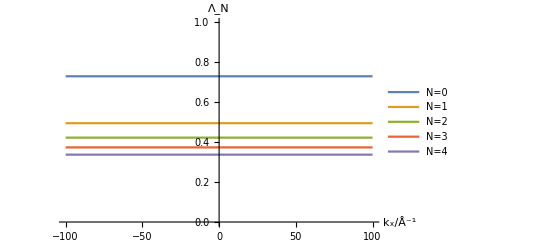

```mathematica
Plot[{y0,y1,y2,y3,y4} ,{x,-100,100},
PlotLegends->{"N=0","N=1","N=2","N=3","N=4"},
PlotRange->{{-100,100},{0,1}},AxesLabel->{Style["  k_x/Å^-1",FontSize->20,FontColor->Black],Style["Λ_N",FontSize->20,FontColor->Black]},
AxesStyle->{Directive[Black,15],Directive[Black,15]},LabelStyle->Larger,MaxRecursion->0,PlotPoints->50]
```